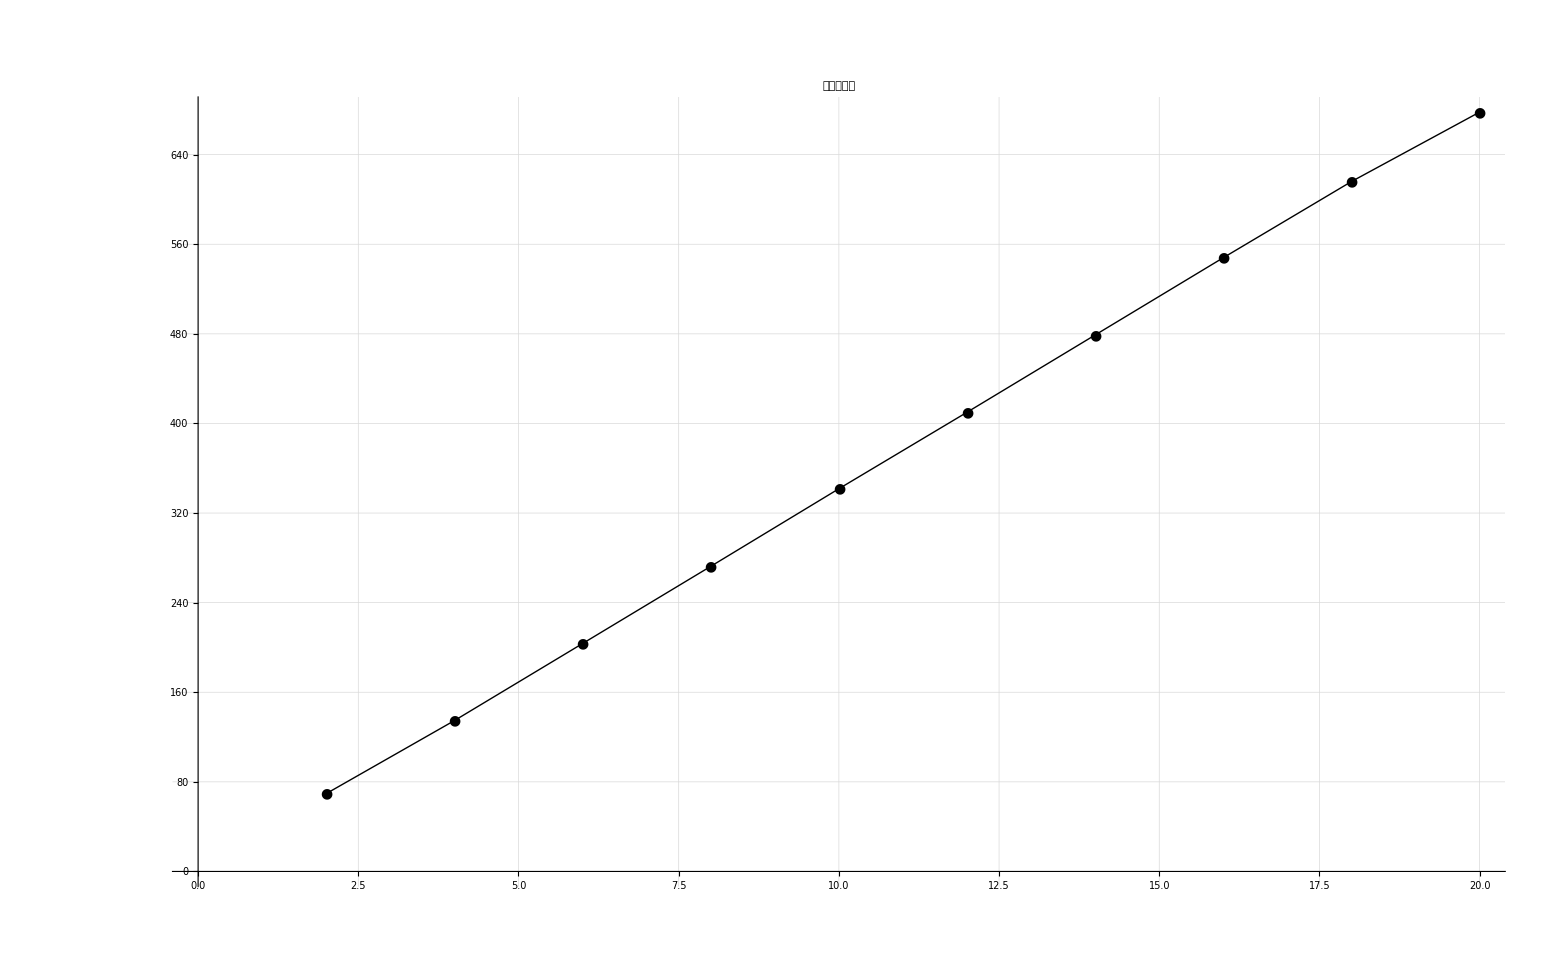

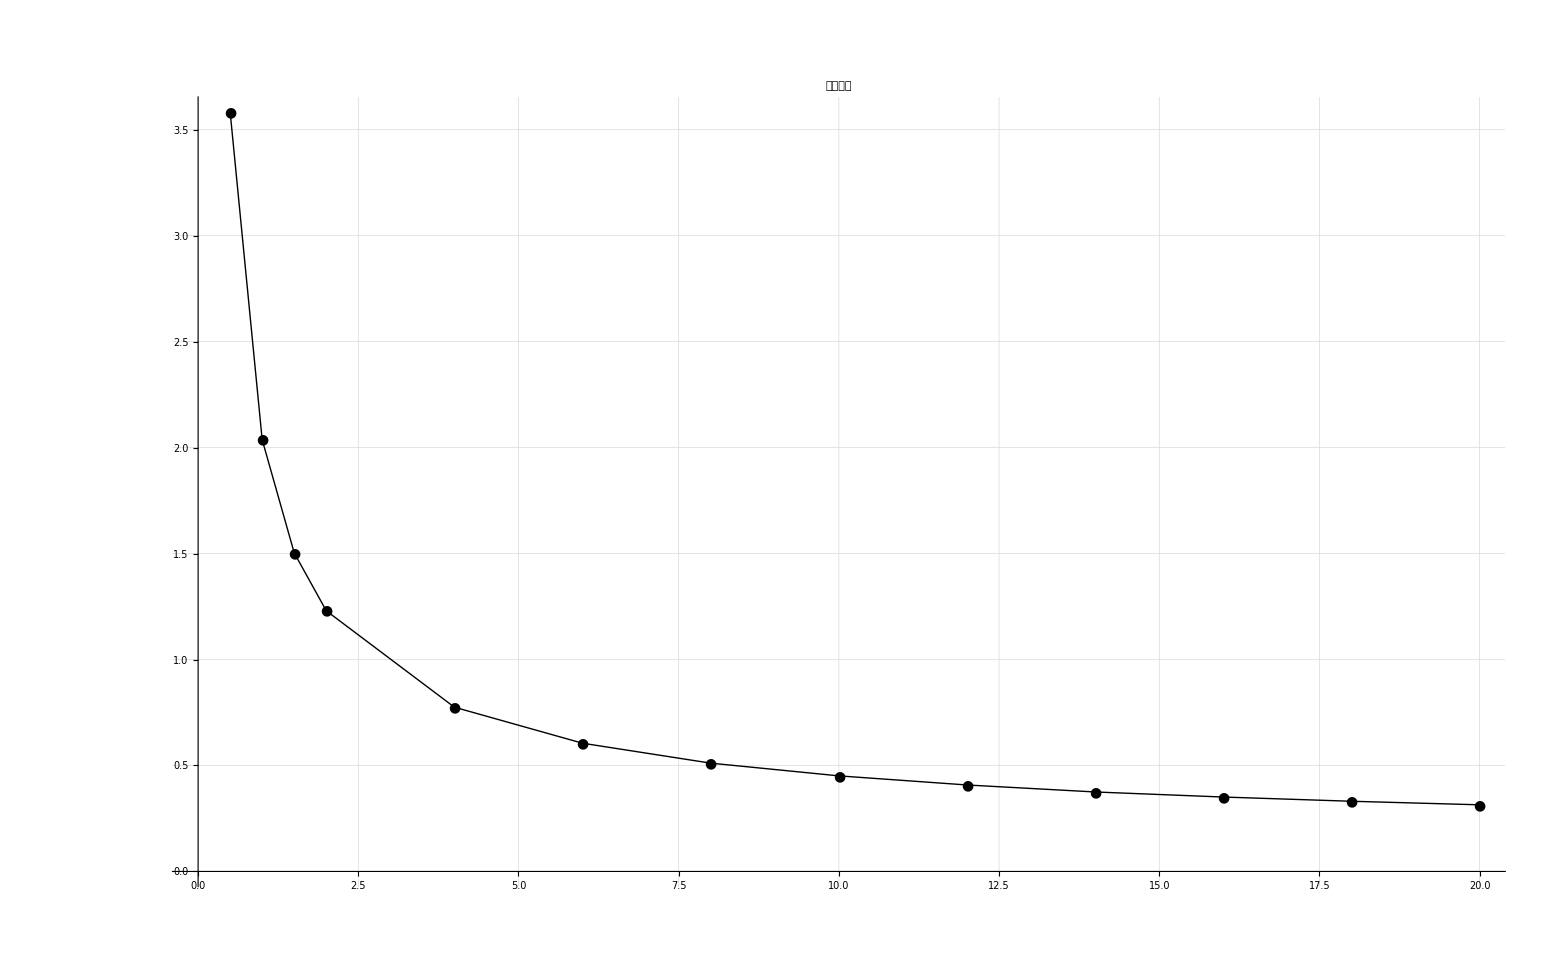

```mathematica
I1=Range[2,20,2];
V={69.5,134.7,203.5,272.4,341.7,410.0,479.0,548.0,616.0,678};
I2={Range[0.5,2,0.5],Range[4,20,2]}//Flatten;
R={3.583,2.037,1.503,1.230,0.775,0.605,0.511,0.451,0.408,0.375,0.3511,0.3312,0.3144};

form2export1={Join[{"I(mA)"},I1],
Join[{"V(mV)"},V]};
form2export2={Join[{"I(mA)"},I2],
Join[{"R(kΩ)"},R]};

Export["~/OneDrive/Medical Sensor/exp5_data1.xlsx",form2export1,"XLSX"];
Export["~/OneDrive/Medical Sensor/exp5_data2.xlsx",form2export2,"XLSX"];

coordinates1=Transpose[{I1,V}];
coordinates2=Transpose[{I2,R}];

PlotGraph=ListLinePlot[
coordinates1,
PlotMarkers->{Automatic,14},
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"I/mA","V/mV"},
PlotLabel->"光电二极管",
BaseStyle->{FontWeight->"Bold",FontSize->18}
]
PlotGraph=ListLinePlot[
coordinates2,
PlotMarkers->{Automatic,14},
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"I/mA","R/kΩ"},
PlotLabel->"光敏电阻",
BaseStyle->{FontWeight->"Bold",FontSize->18}
]
```